# Information Geometry of the Beta Distribution

## Nicholas Wisniewski

```mathematica
a=k;
b=θ;
distribution=PDF[BetaDistribution[a,b],x];
pdfCoords={a,b};
pdfAssumptions={a>0,b>0};
pdfIntegrationLimits={0,1};
```

```mathematica
KL[a1_,b1_,a2_,b2_]:=Log[Beta[a2,b2]/Beta[a1,b1]]-(a2-a1)PolyGamma[a1]-(b2-b1)PolyGamma[b1]+(a2-a1+b2-b1)PolyGamma[a+b];
```

```mathematica
a2+b2=10
```

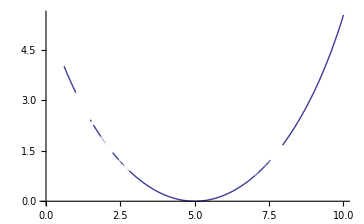

```mathematica
Plot[KL[6,6,a2+1,1+10-a2],{a2,0,10}]
```

```mathematica
distribution
```

Piecewise[{{((1-x)^(-1+θ) x^(-1+k))/Beta[k,θ], 0<x<1}, {0, True}}]

```mathematica
g=FisherMetric[distribution,pdfCoords,pdfAssumptions,pdfIntegrationLimits]
```

{{PolyGamma[1,k]-PolyGamma[1,k+θ],-PolyGamma[1,k+θ]},{-PolyGamma[1,k+θ],PolyGamma[1,θ]-PolyGamma[1,k+θ]}}

```mathematica
Det[g]
```

PolyGamma[1,k] PolyGamma[1,θ]-PolyGamma[1,k] PolyGamma[1,k+θ]-PolyGamma[1,θ] PolyGamma[1,k+θ]

```mathematica
Clear[jeffreys]
```

```mathematica
jeffreys[θ_,k_]:=Sqrt[PolyGamma[1,k] PolyGamma[1,θ]-PolyGamma[1,k] PolyGamma[1,k+θ]-PolyGamma[1,θ] PolyGamma[1,k+θ]]
```

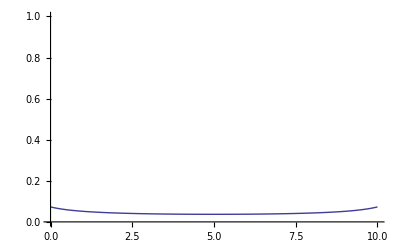

```mathematica
Plot[jeffreys[1+θ,11-θ],{θ,0,10},PlotRange->{0,1}]
```

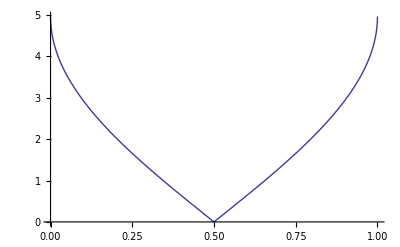

```mathematica
Plot[2 Sqrt[10] ArcCos[Sqrt[.5 ξ]+Sqrt[(1-.5)(1-ξ)]],{ξ,0,1},PlotRange->All]
```

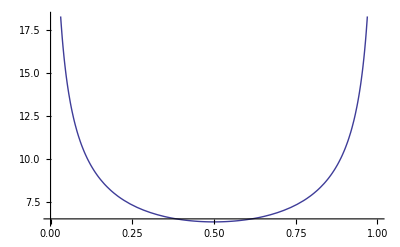

```mathematica
Plot[Sqrt[10/(ξ(1-ξ))],{ξ,0,1}]
```

```mathematica
Γ=LeviCivitaCoefficients[g,pdfCoords]
```

({(1θ (2k-2k+θ)-1k+θ 2k)/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k+θ 2k-1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {(1θ 2k+θ)/(2 (1k+1θ) 1k+θ-2 1k 1θ),-(1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)}
{(1θ 2k+θ)/(2 (1k+1θ) 1k+θ-2 1k 1θ),-(1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {(1k+θ 2θ-1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k (2θ-2k+θ)-1k+θ 2θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)})

```mathematica
Γα=AlphaCoefficients[distribution,g,pdfCoords,pdfAssumptions,pdfIntegrationLimits]
```

({((α-1) (1k+θ 2k+1θ (2k+θ-2k)))/(2 1k 1θ-2 (1k+1θ) 1k+θ),((α-1) (1k 2k+θ-1k+θ 2k))/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {((α-1) 1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),((α-1) 1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)}
{((α-1) 1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),((α-1) 1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {((α-1) (1θ 2k+θ-1k+θ 2θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ),((α-1) (1k+θ 2θ+1k (2k+θ-2θ)))/(2 1k 1θ-2 (1k+1θ) 1k+θ)})

```mathematica
Γα/.{α->0}
Γα/.{α->1}
Γα/.{α->-1}
```

({-(1k+θ 2k+1θ (2k+θ-2k))/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(1k 2k+θ-1k+θ 2k)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {-(1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)}
{-(1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {-(1θ 2k+θ-1k+θ 2θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(1k+θ 2θ+1k (2k+θ-2θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ)})

({0,0} | {0,0}
{0,0} | {0,0})

({-(2 (1k+θ 2k+1θ (2k+θ-2k)))/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(2 (1k 2k+θ-1k+θ 2k))/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {-(2 1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(2 1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)}
{-(2 1θ 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(2 1k 2k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)} | {-(2 (1θ 2k+θ-1k+θ 2θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ),-(2 (1k+θ 2θ+1k (2k+θ-2θ)))/(2 1k 1θ-2 (1k+1θ) 1k+θ)})

```mathematica
Ruplijk=RiemannTensor1[Γα,pdfCoords]
```

((0 | -((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2)
((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | 0) | (0 | -((α^2-1) (1θ-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2)
((α^2-1) (1θ-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | 0)
(0 | ((α^2-1) (1k-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2)
-((α^2-1) (1k-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | 0) | (0 | ((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2)
-((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | 0))

```mathematica
Rdownlijk=RiemannTensor2[Γα,g,pdfCoords]
```

((0 | 0
0 | 0) | (0 | ((α^2-1) (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 1k 1θ-4 (1k+1θ) 1k+θ)
((α^2-1) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 1k 1θ-4 (1k+1θ) 1k+θ) | 0)
(0 | ((α^2-1) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 1k 1θ-4 (1k+1θ) 1k+θ)
((α^2-1) (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 1k 1θ-4 (1k+1θ) 1k+θ) | 0) | (0 | 0
0 | 0))

```mathematica
Rij=RicciTensor[Ruplijk,pdfCoords]
```

(-((α^2-1) (1k-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | -((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2)
-((α^2-1) 1k+θ (1k+θ 2k 2θ-(1θ 2k+1k 2θ) 2k+θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2) | -((α^2-1) (1θ-1k+θ) ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))/(4 (1k 1θ-(1k+1θ) 1k+θ)^2))

```mathematica
R=ScalarCurvature[Rij,g,pdfCoords]
```

-((α^2-1) (2k 2θ 1k+θ-(2k 1θ+1k 2θ) 2k+θ) (1k+θ)^2)/(2 (1k 1θ-1θ 1k+θ-1k 1k+θ) (1k 1θ-(1k+1θ) 1k+θ)^2)-((α^2-1) (1k-1k+θ) (1θ-1k+θ) ((2k 1θ+1k 2θ) 2k+θ-2k 2θ 1k+θ))/(2 (1k 1θ-1θ 1k+θ-1k 1k+θ) (1k 1θ-(1k+1θ) 1k+θ)^2)

```mathematica
Solve[R==0,{α}]
```

{{α→-1},{α→1}}

```mathematica
geodesics=EulerLagrangeEquations[Γα,pdfCoords,t]
```

{k''(t)+((α-1) (1θ 2k+θ (k'(t)+θ'(t))^2+2k (-1θ) (k'(t))^2+2k (k'(t))^2 1k+θ-2θ 1k+θ (θ'(t))^2))/(2 1k 1θ-2 (1k+1θ) 1k+θ),((α-1) (1k 2k+θ (k'(t)+θ'(t))^2+2k (k'(t))^2 (-1k+θ)-1k 2θ (θ'(t))^2+2θ 1k+θ (θ'(t))^2))/(2 1k 1θ-2 (1k+1θ) 1k+θ)+θ''(t)}

```mathematica
geodesics/.{α->0}//FullSimplify
geodesics/.{α->1}//FullSimplify
geodesics/.{α->-1}//FullSimplify
```

{k''(t)+(-1θ 2k+θ (k'(t)+θ'(t))^2+2k 1θ (k'(t))^2-2k (k'(t))^2 1k+θ+2θ 1k+θ (θ'(t))^2)/(2 1k 1θ-2 (1k+1θ) 1k+θ),(-1k 2k+θ (k'(t)+θ'(t))^2+2k (k'(t))^2 1k+θ+1k 2θ (θ'(t))^2-2θ 1k+θ (θ'(t))^2)/(2 1k 1θ-2 (1k+1θ) 1k+θ)+θ''(t)}

{k''(t),θ''(t)}

{k''(t)+(-1θ 2k+θ (k'(t)+θ'(t))^2+2k 1θ (k'(t))^2-2k (k'(t))^2 1k+θ+2θ 1k+θ (θ'(t))^2)/(1k 1θ-(1k+1θ) 1k+θ),(-1k 2k+θ (k'(t)+θ'(t))^2+2k (k'(t))^2 1k+θ+1k 2θ (θ'(t))^2-2θ 1k+θ (θ'(t))^2)/(1k 1θ-(1k+1θ) 1k+θ)+θ''(t)}

```mathematica
einstein=EinsteinTensor[Rij,g,R,pdfCoords]
```

(((1θ-1k+θ) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2+(α^2-1) 1k+θ 2k 2θ-(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)-(α^2-1) 2θ 2k+θ)) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2-(α^2-1) 1k+θ 2k 2θ+(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)+(α^2-1) 2θ 2k+θ)))/(4 (α^2-1) ((1k+1θ) 1k+θ-1k 1θ)^3 ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ)) | -(1k+θ (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2+(α^2-1) 1k+θ 2k 2θ-(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)-(α^2-1) 2θ 2k+θ)) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2-(α^2-1) 1k+θ 2k 2θ+(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)+(α^2-1) 2θ 2k+θ)))/(4 (α^2-1) (1k 1θ-(1k+1θ) 1k+θ)^3 ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ))
-(1k+θ (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2+(α^2-1) 1k+θ 2k 2θ-(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)-(α^2-1) 2θ 2k+θ)) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2-(α^2-1) 1k+θ 2k 2θ+(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)+(α^2-1) 2θ 2k+θ)))/(4 (α^2-1) (1k 1θ-(1k+1θ) 1k+θ)^3 ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ)) | ((1k-1k+θ) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2+(α^2-1) 1k+θ 2k 2θ-(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)-(α^2-1) 2θ 2k+θ)) (4 (1k)^2 (1θ-1k+θ)^2+4 (1θ)^2 (1k+θ)^2-(α^2-1) 1k+θ 2k 2θ+(α^2-1) 1θ 2k 2k+θ+1k (8 1θ 1k+θ (1k+θ-1θ)+(α^2-1) 2θ 2k+θ)))/(4 (α^2-1) ((1k+1θ) 1k+θ-1k 1θ)^3 ((1θ 2k+1k 2θ) 2k+θ-1k+θ 2k 2θ)))

```mathematica
covderiv=CovariantDerivative[{a,b},Γα,pdfCoords]
```

{((α-1) 1k+θ (k 2k-θ 2θ)+1θ ((α-1) (2 (k+θ) 2k+θ-k 2k)-2 1k+θ)+2 1k (1θ-1k+θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k+θ (-(α-1) (k 2k-θ 2θ)-2 1θ)+1k ((α-1) (2 (k+θ) 2k+θ-θ 2θ)-2 1k+θ+2 1θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ)}

```mathematica
covderiv/.{α->0}
covderiv/.{α->1}
covderiv/.{α->-1}
```

{(2 1k (1θ-1k+θ)-1k+θ (k 2k-θ 2θ)+1θ (-2 1k+θ-2 (k+θ) 2k+θ+k 2k))/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k+θ (k 2k-2 1θ-θ 2θ)+1k (-2 1k+θ-2 (k+θ) 2k+θ+2 1θ+θ 2θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ)}

{(2 1k (1θ-1k+θ)-2 1θ 1k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k (2 1θ-2 1k+θ)-2 1θ 1k+θ)/(2 1k 1θ-2 (1k+1θ) 1k+θ)}

{(2 1k (1θ-1k+θ)-2 1k+θ (k 2k-θ 2θ)+1θ (-2 1k+θ-2 (2 (k+θ) 2k+θ-k 2k)))/(2 1k 1θ-2 (1k+1θ) 1k+θ),(1k+θ (2 (k 2k-θ 2θ)-2 1θ)+1k (-2 1k+θ-2 (2 (k+θ) 2k+θ-θ 2θ)+2 1θ))/(2 1k 1θ-2 (1k+1θ) 1k+θ)}